```mathematica
Fooling Functions
```

Fooling Functions

```mathematica
For Integration
```

For Integration

```mathematica
f1[x_]=30*x^2(1-x)^2
```

30 (1-x)^2 x^2

```mathematica
Integrate[f1[x],{x,0,1}]
```

1

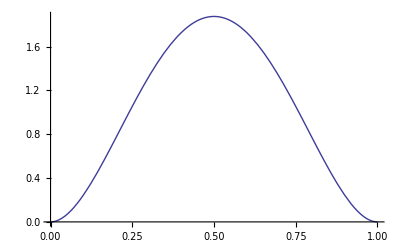

```mathematica
Plot[f1[x],{x,0,1}]
```

```mathematica
f1p[x_]=Factor[D[f1[x],x]]
```

60 (-1+x) x (-1+2 x)

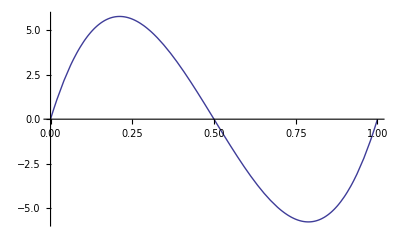

```mathematica
Plot[f1p[x],{x,0,1}]
```

```mathematica
f1p1norm=Integrate[f1p[x],{x,0,1/2}]-Integrate[f1p[x],{x,1/2,1}]
```

15/4

```mathematica
f1pp[x_]=Factor[D[f1p[x],x]]
```

60 (1-6 x+6 x^2)

```mathematica
Solve[f1pp[x]==0,x]
```

{{x→1/6 (3-√3)},{x→1/6 (3+√3)}}

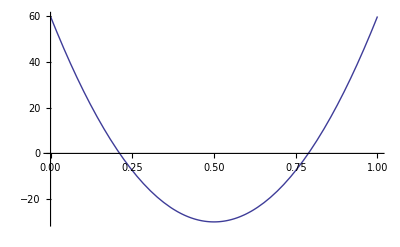

```mathematica
Plot[f1pp[x],{x,0,1}]
```

```mathematica
f1p1norm=Integrate[f1pp[x],{x,0,1/2-Sqrt[3]/6}]-Integrate[f1pp[x],{x,1/2-Sqrt[3]/6,1/2+Sqrt[3]/6}]+ Integrate[f1pp[x],{x,1/2+Sqrt[3]/6,1}]
```

40/(√3)

```mathematica
For Approximation
```

Approximation For

```mathematica
f1[x_]=16*x^2(1-x)^2
```

16 (1-x)^2 x^2

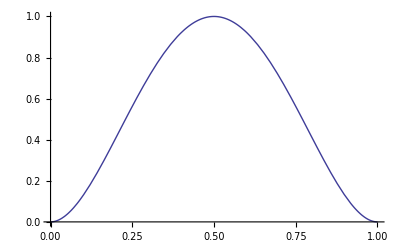

```mathematica
Plot[f1[x],{x,0,1}]
```

```mathematica
Maximize[{f1[x], x ≥0,x ≤ 1},x]
```

{1,{x→1/2}}

```mathematica
f1p[x_]=Factor[D[f1[x],x]]
```

32 (-1+x) x (-1+2 x)

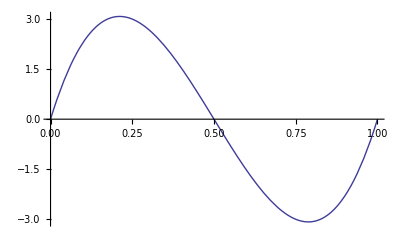

```mathematica
Plot[f1p[x],{x,0,1}]
```

```mathematica
f1pinfnorm=Simplify[Maximize[{Abs[f1p[x]], x ≥0,x ≤ 1},x]]
```

{16/(3 √3),{x→1/6 (3+√3)}}

```mathematica
f1pp[x_]=Factor[D[f1p[x],x]]
```

32 (1-6 x+6 x^2)

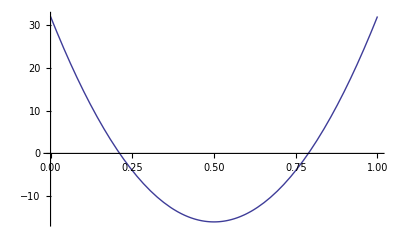

```mathematica
Plot[f1pp[x],{x,0,1}]
```

```mathematica
f1ppinfnorm=Simplify[Maximize[{Abs[f1pp[x]], x ≥0,x ≤ 1},x]]
```

{32,{x→0}}